## Calculations for integral control instability problem (Problem 3.5)

Part b

```mathematica
poly=s(1+s)^2+4/27 // Apart
```

4/27+s+2 s^2+s^3

```mathematica
p1=Factor[poly]
```

1/27 (1+3 s)^2 (4+3 s)

There are 2 roots at s=-1/3 and one root at s=-4/3.

```mathematica
p2lhs=s(s+1)^2+Ki // Apart
```

Ki+s+2 s^2+s^3

```mathematica
p2rhs=(s+p)^2(s+q) // Apart
```

p^2 q+p (p+2 q) s+(2 p+q) s^2+s^3

```mathematica
Solve[p2lhs==p2rhs,{Ki,p,q}]//Simplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Ki→p^2 (q+s)+2 p s (q+s)+s (-1+(-2+q) s)}}

Part c

```mathematica
sol1=Solve[ω^2((1-ω^2)^2+4 ω^2)-Ki^2==0,ω][[1]] // Simplify
```

{ω→(2 3^(1/3)-2^(1/3) (-9 Ki+√(12+81 Ki^2))^(2/3))/(6^(2/3) (-9 Ki+√(12+81 Ki^2))^(1/3))}

```mathematica
Subscript[ω, 0]=ω/.sol1;
θ=ArcTan[2 Subscript[ω, 0],1-Subscript[ω, 0]^2] // FullSimplify
```

ArcTan[(2 6^(1/3)-2^(2/3) (-9 Ki+√(12+81 Ki^2))^(2/3))/(3^(2/3) (-9 Ki+√(12+81 Ki^2))^(1/3)),1-((-2 3^(1/3)+2^(1/3) (-9 Ki+√(12+81 Ki^2))^(2/3))^2)/(6 6^(1/3) (-9 Ki+√(12+81 Ki^2))^(2/3))]

Part d

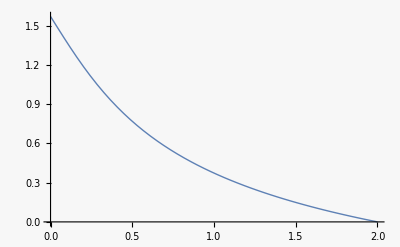

```mathematica
plot0=Plot[θ,{Ki,0,2}]
```

```mathematica
tmax=2;dt=0.01;
dat=Table[{Ki,θ},{Ki,0,tmax,dt}];
(* SetDirectory[NotebookDirectory[]] *)
```

```mathematica
(* Export["integral_control_instability_out.dat", dat] *)
```

PhaseMargins::notfound: Symbol Ki not found.

Join::heads: Heads List and PhaseMargins at positions 1 and 2 are expected to be the same.

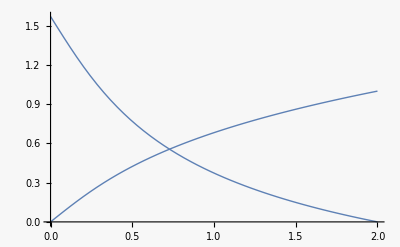

```mathematica
looptf=TransferFunctionModel[1/(1+s)^2 Ki/s,s];
pm=PhaseMargins[looptf];
Plot[pm,{Ki,0,2}]
```

GainMargins::notfound: Symbol Ki not found.

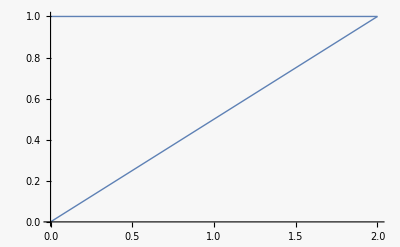

```mathematica
gm=GainMargins[looptf];
Plot[1/gm,{Ki,0,2}]
```

```mathematica
N[pm/.Ki->1][[1,2]] 180/π
```

PhaseMargins::notfound: Symbol Ki not found.

21.3864